# Getting Started with MathOptimizer

## Frank J. Kampas and János D. Pintér

### Summary

This document serves as a brief introduction to using MathOptimizer. A more detailed description is presented in the User Guide which should be consulted for technical background and references, further examples and applications.

MathOptimizer is an integrated global-local optimization package for handling difficult nonlinear optimization problems. Specifically, when its global search is invoked then it aims to find the globally best solution in (possibly) multimodal problems with multiple extrema. Using MathOptimizer "only" in its local search mode allows to find the best solution from a given starting point that, alternatively, can also be set by default.

In principle, MathOptimizer can handle optimization models defined by arbitrary continuous functions, without requiring gradient or higher-order analytical information. Formally, we consider the general model type

minimize f(x)

subject to the constraints

g(x) ≤ 0

xlb ≤ x ≤ xub

Here x is an n-dimensional real vector, f is a scalar objective function, and g is an m-component real-valued vector function. We shall assume (require) that the component-wise bounds xlb and xub are finite, and that f and g (the latter component-wise) are continuous. Let us point out that all well-posed, but seemingly more general finite-dimensional constrained optimization models can be brought to the above canonical form by (elementary or more advanced) transformations.

The model functions themselves can be defined using Mathematica's extensive related capabilities. This feature supports a very broad range of model development options.

### MathOptimizer Platform

MathOptimizer can be used with Mathematica version 5.2 and higher, across all platforms for which Mathematica implementations exist.

```mathematica
$Version
```

7.0 for Microsoft Windows (32-bit) (February 18, 2009)

```mathematica
Date[]
```

{2009,10,25,15,24,20.5521901}

The test results and optional timings reported below were obtained using our various (as of 2009, average capacity) personal computers. All models presented in this document solve in a second or less, except the numerically more intensive parametric integral optimization model described in the section titled "Optimization of Models with User-Defined Functions".

### Install and Launch MathOptimizer

The installer should input $UserAddOnsDirectory into Mathematica and put the MathOptimizer directory into the directory that is returned. 
The $UserAddOnsDirectory may be hidden, requiring the installer to check "Show Hidden Files" or something similar when looking for it. 
For example, in Suse Linux, $UserAddOnsDirectory is /home/<UserName>/.Mathematica.
Then MathOptimizer can be directly invoked for use by the following statement.

```mathematica
Needs["MathOptimizer`MO`"]
```

The next statement serves only to verify the availability of MathOptimizer's integrated MO package.

```mathematica
$ContextPath
```

{MathOptimizer`MO`,PacletManager`,WebServices`,System`,Global`}

```mathematica
?Optimize
```

Optimize[objective, constraints_List, varswithbounds_List, options___] 
minimizes the given objective function under a given set (list) of constraint functions, and 
given variable bounds. The varswithbounds list is defined in the form 
{{var1, var1 lower bound, var1 upper bound}, {var2, var2 lower bound, var2 upper bound}...}.
Type Options[Optimize] to see the options and their default settings.  
Type ?optionname for more information on each individual option.

The Optimize function requires three key arguments:  the model objective function, the list of model constraints, and the list of decision variables with corresponding bounds.  A number of options can be selected and added to the input list: we will discuss each of the options later on.

Notice that this structure is a bit different from that of NMinimize, which has the objective function as the first argument of a list containing the objective function and the constraints.

Optimize returns a list containing the objective function value at the numerical optimum found, a list of rules giving the variable values, and the maximum constraint violation, which is given as 0 is there are no constraints.

### MathOptimizer Options

We wish to emphasize that although the global search approaches implemented in MathOptimizer are theoretically globally convergent (with probability 1), in numerical practice it could occur that the optimum of a difficult model is not found directly, applying default option settings and a limited numerical effort. Evidently, the same applies to all numerical optimization algorithm implementations. Many of the examples discussed in detail by the MathOptimizer User's Guide suggest option settings to overcome this inherent difficulty. Generally speaking, in "relatively easy" models, one can expect that all reasonable option settings will generate the same global optimum estimate (except small numerical differences). This finding is confirmed by our extensive numerical optimization benchmarking studies. In "more difficult" models, option changes may lead to a range of numerical solutions, and the user can eventually select the best one found.

```mathematica
Options[Optimize]
```

{PenaltyMultiplier→1,MultiStarts→10,Samples→1000,RandomSeed→0,SamplingMethod→Random,ListableExpressions→True,LocalSearches→4,ShowGlobalResults→False,ShowDetailedGlobalResults→False,ShowLocalResults→False,ShowDetailedLocalResults→False,LocalSearchMethod→FindMinimum,BoundedLocalSearch→True,RepeatedLocalSearches→True}

All default option settings can be overruled (changed) using standard Mathematica conventions.  This point is extensively illustrated by detailed examples in the MathOptimizer User's Guide.

### Illustrative Examples

#### A Box-Constrained Model

If there are no constraints, then the second argument of Optimize is an empy list as shown below.

```mathematica
Optimize[(x-1)^2+(y-2)^2,{},{{x,-5,5},{y,-5,5}}]
```

{9.2968×10^-26,{x→1.,y→2.},Maximal Constraint Violation→0}

Optimize returns a list containing the objective function value at the numerical optimum found, a list of rules giving the optimized values for the decision variables, and the maximum constraint violation at the numerical optimum. (The latter should be 0 here, since there are no constraints.)

#### Excplicit Variable Bounds

The stated variable bounds are strictly enforced by MathOptimizer in its default mode, as shown by the next example. This is another difference with NMinimize, in which variable bounds are not required, and thus the search range is set only when explicitly defined.

```mathematica
Optimize[(x-6)^2+(y-2)^2,{},{{x,-5,5},{y,-5,5}}]
```

{1.,{x→5.,y→2.},Maximal Constraint Violation→0}

```mathematica
NMinimize[(x-6)^2+(y-2)^2,{{x,-5,5},{y,-5,5}}]
```

{0.,{x→6.,y→2.}}

Let us remark here again that – in a mathematically precise setting – one does need variable bounds and continuous model functions to guarantee that a general global optimization problem in itself is well-posed.  The continuity assumptions can be replaced by somewhat milder analytical conditions that will not be discussed here, since continuity is most typically satisfied in the prospective domain of MathOptimizer applications.

It is also noted that, in general, tighter variable bounds can lead to better (sometimes much better) numerical performance: therefore it is worthwile to give proper consideration to all variable bound settings.

#### Initial Variable Values

It is possible to give initial values for some or all of the variables. If such a value is not given, then the midpoint (component-wise central point) of the interval defined by the bounds is used by default. The initial values of the variables are used as one set of starting values for the local search – quite possibly together with some further initial points generated, as will be discussed and illustrated later on.

```mathematica
Optimize[(x-1)^2+(y-2)^2,{},{{x,-5,4,5},{y,-5,3,5}}]
```

{9.2968×10^-26,{x→1.,y→2.},Maximal Constraint Violation→0}

#### Equality and Inequality Constraints

If the constraints are all inequalities, then it is possible – but not necessarily guaranteed – that the maximum constraint violation will be 0.

```mathematica
Optimize[(x-1)^2+(y-2)^2,{x+y≤ 3},{{x,-2,5},{y,-1,3}}]
```

{4.05963×10^-7,{x→0.999549,y→1.99955},Maximal Constraint Violation→0.}

If equality constraints are also present, then one can expect corresponding small constraint violations, especially if the exact solution vector has non-rational number components. To illustrate, in the following example the optimal values for both x and y are -√(1/2)~ -0.707107 which cannot be represented as a machine number.

```mathematica
Optimize[x+y,{x^2+y^2≤ 1},{{x,-1,1},{y,-1,1}}]
```

{-1.41421,{x→-0.707106,y→-0.707108},Maximal Constraint Violation→1.16707×10^-7}

```mathematica
Optimize[x+y,{x^2+y^2==1},{{x,-1,1},{y,-1,1}}]
```

{-1.41421,{x→-0.707106,y→-0.707108},Maximal Constraint Violation→2.51329×10^-7}

#### Model Development Step-by-Step

It is easy to modify the objective function or a constraint, to add new constraints, or to change the model functions otherwise in a stepwise fashion. This feature makes modular development easy, as illustrated by the sequence of models shown below. Model changes can also be made simultaneously, of course.

```mathematica
Optimize[(x-1)^2+(y-2)^2,{x-y≥1},{{x,-5,4,5},{y,-5,3,5}}]
```

{2.,{x→2.,y→1.},Maximal Constraint Violation→0.}

```mathematica
Optimize[(x-1)^2+(y-2)^2,{x-y≥1, Sin[2*y]-Cos[x^2]≥1 },{{x,-5,4,5},{y,-5,3,5}}]
```

{2.,{x→2.,y→1.},Maximal Constraint Violation→0.}

```mathematica
Optimize[(x-1)^2+(y-2)^2,{x-y≥1, Sin[2*y]-Cos[x^2]==1 },{{x,-5,4,5},{y,-5,3,5}}]
```

{2.77882,{x→1.37597,y→0.375972},Maximal Constraint Violation→4.57071×10^-8}

```mathematica
Optimize[(x-1)^2+(y-2)^2 + Sin[2*y]-Cos[x^2],{x-y≥1, Sin[2*y]-Cos[x^2]==1 },{{x,-5,4,5},{y,-5,3,5}}]
```

{3.77882,{x→1.37597,y→0.375972},Maximal Constraint Violation→5.79773×10^-8}

```mathematica
Optimize[(x-1)^2+(y-2)^2 + Sin[2*y]-Cos[x^2],{x-y≥0.4, x-y≤0.8,Sin[2*y]-Cos[x^2]==1 },{{x,-5,4,5},{y,-5,3,5}}]
```

{2.37172,{x→1.25744,y→0.857441},Maximal Constraint Violation→1.61865×10^-8}

#### A Model Development Template

The next example shows an easy-to-use model development template.

According to the input information requirements of MathOptimizer, we define the following model components:

varswithbounds: the decision variables with lower and upper bounds, nominal values can be optionally added

objective: the model objective function to minimize

constraints: the model constraints.

```mathematica
varswithbounds = {{x1, -5, 3}, {x2, -5, 4}}; 	
objective = (x1^2 - 2*x2)^2 + (x1 - 2)^2; 
constraints = {Sin[x1^2 - 3*x1*x2] == 0, x1^4 + 5*x2^3 - 40 ≤ 0};
```

```mathematica
objective 
constraints 
varswithbounds
```

(-2+x1)^2+(x1^2-2 x2)^2

{Sin[x1^2-3 x1 x2]==0,-40+x1^4+5 x2^3≤0}

{{x1,-5,3},{x2,-5,4}}

```mathematica
Optimize[objective, constraints, varswithbounds]
```

{0.0166185,{x1→1.87448,x2→1.74215},Maximal Constraint Violation→1.80328×10^-10}

In spite of its small size, this model is not trivial. For comparison, let us solve the same model using the built-in function NMinimize. To this end, we introduce the auxiliary symbols

```mathematica
vars = { x1,x2}
Flatten[{objective, constraints}]
```

{x1,x2}

{(-2+x1)^2+(x1^2-2 x2)^2,Sin[x1^2-3 x1 x2]==0,-40+x1^4+5 x2^3≤0}

```mathematica
NMinimize[Flatten[{objective, constraints}], vars]
```

{1.03074,{x1→1.13774,x2→0.379247}}

The solution found by NMinimize is not as good as MathOptimizer's solution. This is not always the case, of course. However, the example illustrates an important point: using different approaches (algorithms and corresponding software implementations) to solve difficult numerical problems can be useful – especially so in the area of nonlinear optimization.

#### Optimization Models with Arbitrary (Continuous) Mathematica Functions

MathOptimizer can handle user-defined model functions applying Mathematica's rich function repertoire.  In principle, one could use all computable Mathematica functions as model components; for convergence considerations (minimally) the continuity of the model functions is desirable, however.

A technical consideration is to define the model functions so that they are only evaluated numerically, and for safety (i.e., if in doubt, then) to set ListableExpressions to False.

In the next example, we optimize the parameter a in a parametric integral; then we compare our result to the one obtained by NMinimize.

```mathematica
f[a_?NumberQ]:= NIntegrate[Cos[a x^2]*Sin[a x],{x,0,π}]
```

```mathematica
Timing @ NMinimize[{f[a],0 ≤ a ≤ 3},{a}]
```

{51.745,{0.00601389,{a→1.42484}}}

```mathematica
Timing @ Optimize[f[a],{},{{a,0,3}},ListableExpressions -> False, MultiStarts -> 1]
```

{142.382,{-0.293604,{a→0.465361},Maximal Constraint Violation→0}}

Notice that in this example MathOptimizer finds the correct global solution (unlike NMinimize) as shown by the figure below. To generate the figure itself takes some time, due to the embedded integration procedure.

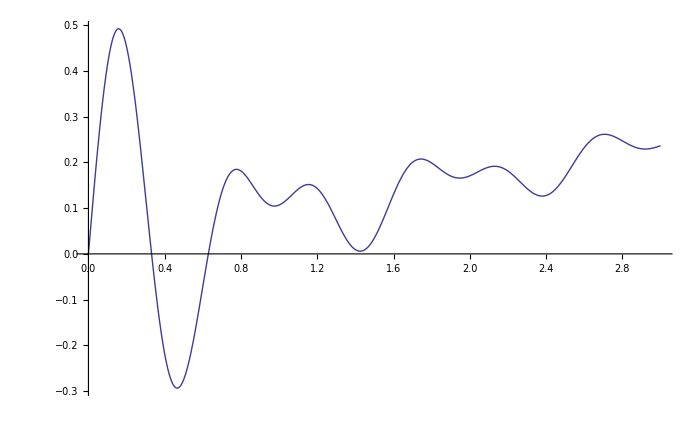
{19.765,-Graphics-}

```mathematica
Timing[Plot[f[a],{a,0,3}]]
```

The runtime to solve this model is about 2.7 times higher for MathOptimizer than for NMinimize. This is not always the case, of course, as it has been extensively illustrated elsewhere in our articles and presentations.

### Further Details and Contact Information

For further details, please consult the complete User Guide accompanying MathOptimizer.

Thanks for your interest.

Frank Kampas, PhD, MBA <fkampas@msn.com>
János Pintér, PhD, DSc <janos.d.pinter@gmail.com>